# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Entropy/schmidt modes/QMB.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

# T1

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=3;
g=10^(-4.);
h=3;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

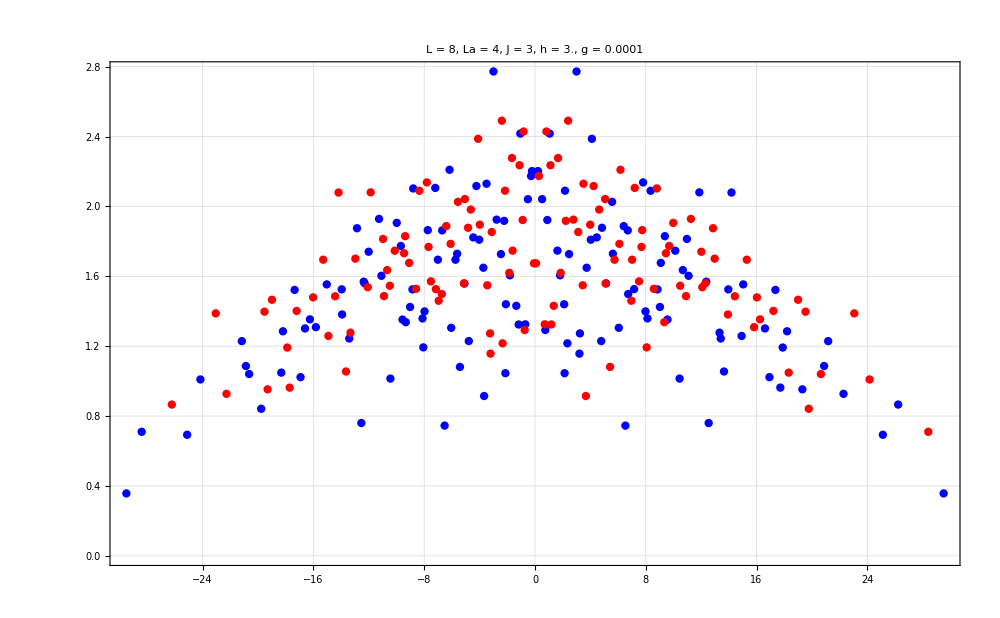

```mathematica
ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

# SVD

```mathematica
Clear[arrayt];
arrayt[t_,val_,vec_]:=Exp[-I*val*t]*vec;
Clear[new];
new[ini_,t_,L_,val_,vec_]:=Module[{schmidt,psit,ck=Conjugate[vec] . ini,d=2^(L/2),phases=arrayt[t,val,vec]},
psit=ArrayReshape[N[Total[ phases*ck  ]],{d,d}];
schmidt=Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]
];
```

```mathematica
allstates=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]][[-10;;-1]];
```

```mathematica
tlist=Table[10^i,{i,0,7,0.0005}];
tlist//Length
```

14001

```mathematica
entropy2=ParallelTable[{t,new[j,t,L,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

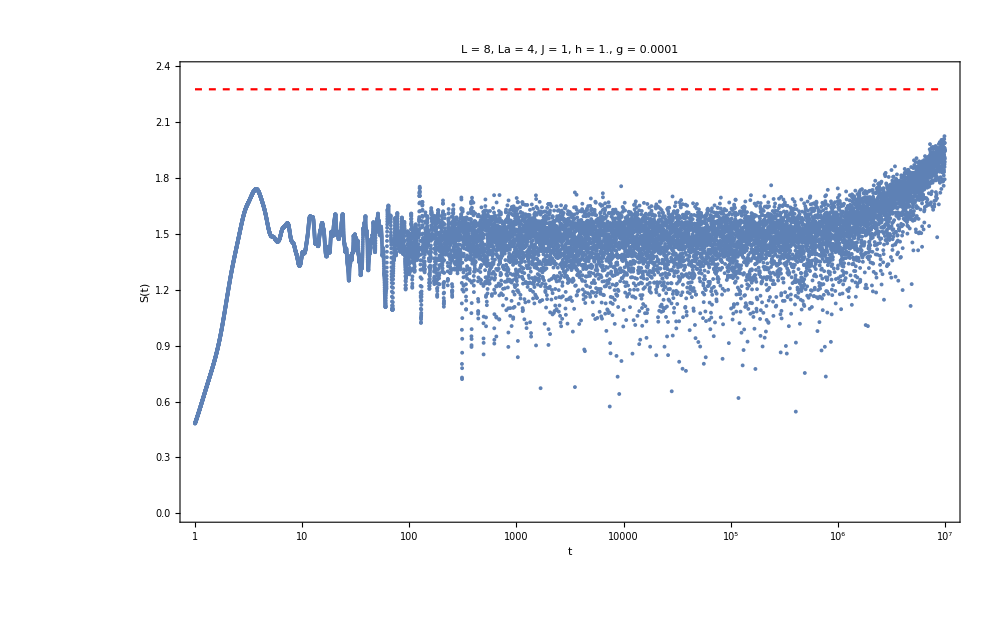

```mathematica
Show[{ListLogLinearPlot[Mean[entropy2],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.1}},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}]
```

## Cycle

```mathematica
J=1;
h=1;
```

```mathematica
glist=Table[10^i,{i,-4,0,0.05}];
glist//Length
```

81

```mathematica
tlist=Table[10^i,{i,0,7,0.001}];
tlist//Length
```

7001

```mathematica
plots={};
plots2={};
Do[

H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

allstates=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]][[-10;;-1]];

entropy2=ParallelTable[{t,new[j,t,L,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];

plot2=Show[{ListLogLinearPlot[Mean[entropy2],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.1}},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}];
Export["mean_plots_L_"<>ToString[L]<>"_h_1_g_"<>ToString[N[g]]<>"_.png",plot2];
AppendTo[plots2,plot2];

,{g,glist}];
```

```mathematica
ListAnimate[plots2,AnimationRunning->False]
```

# SVD 1 spin vs 7

```mathematica
Clear[arrayt];
arrayt[t_,val_,vec_]:=Exp[-I*val*t]*vec;
Clear[new];
new[ini_,t_,La_,val_,vec_]:=Module[{schmidt,psit,ck=Conjugate[vec] . ini,a=2^(La),b=2^(L-La),phases=arrayt[t,val,vec]},
psit=ArrayReshape[N[Total[ phases*ck  ]],{a,b}];
schmidt=Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]
];
```

```mathematica
allstates=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]][[-5;;-1]];
```

```mathematica
tlist=Table[10^i,{i,0,7,0.001}];
tlist//Length
```

7001

```mathematica
entropy1=ParallelTable[{t,new[j,t,1,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
entropy2=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

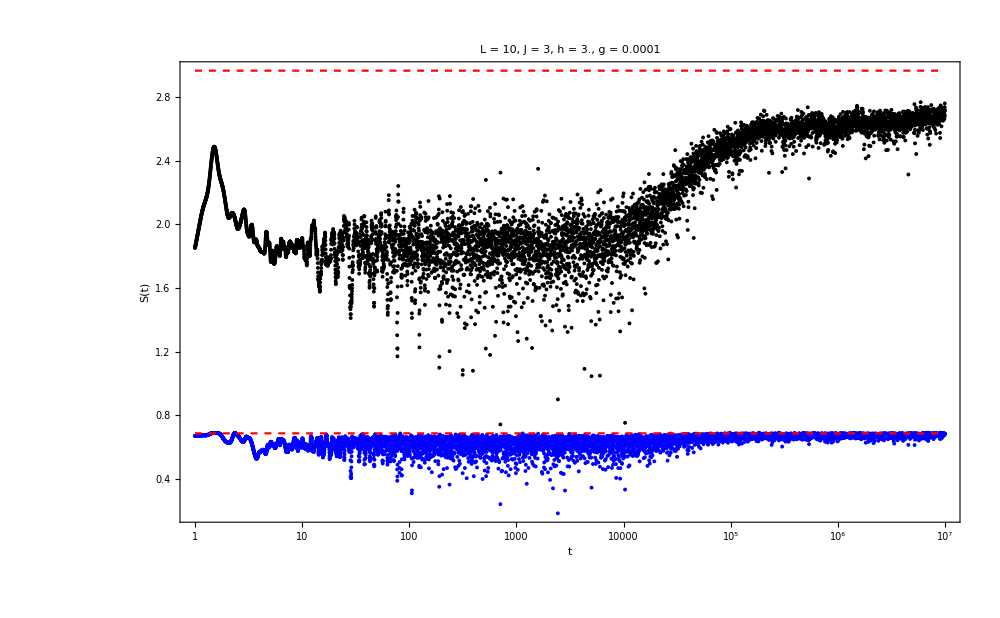

```mathematica
Show[{ListLogLinearPlot[Mean[entropy1],PlotStyle->Blue,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],ListLogLinearPlot[Mean[entropy2],PlotStyle->Black,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[{pageEntropy[1,7],pageEntropy[L/2,L/2]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

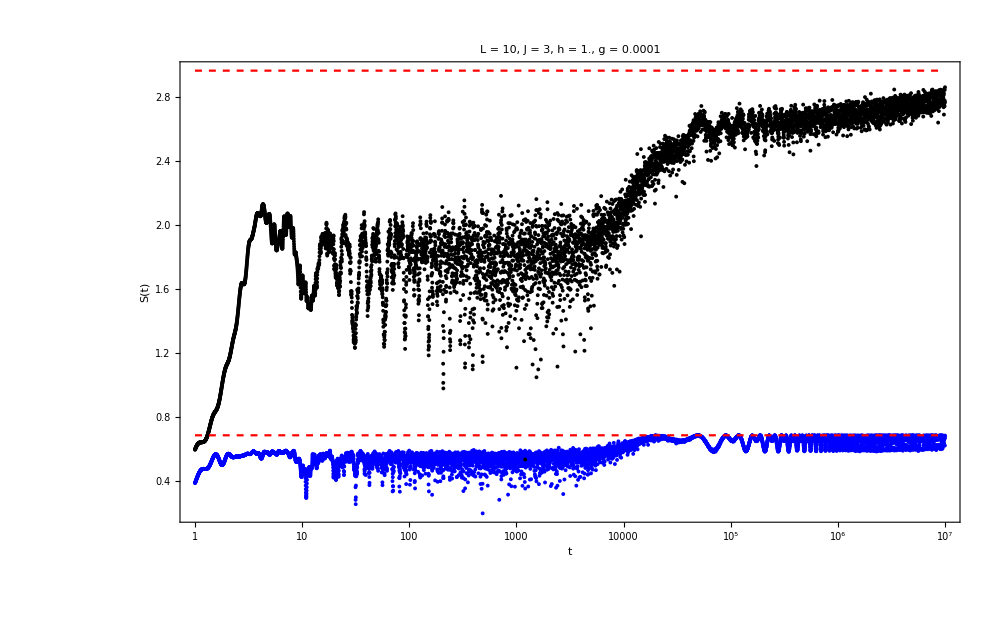

```mathematica
Show[{ListLogLinearPlot[Mean[entropy1],PlotStyle->Blue,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],ListLogLinearPlot[Mean[entropy2],PlotStyle->Black,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[{pageEntropy[1,7],pageEntropy[L/2,L/2]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

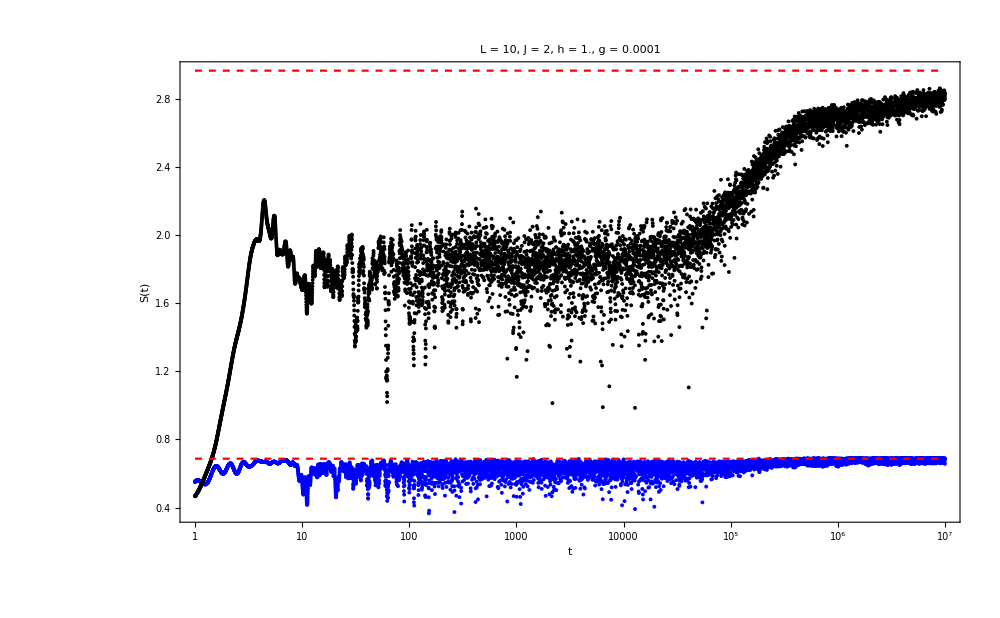

```mathematica
Show[{ListLogLinearPlot[Mean[entropy1],PlotStyle->Blue,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],ListLogLinearPlot[Mean[entropy2],PlotStyle->Black,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[{pageEntropy[1,7],pageEntropy[L/2,L/2]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

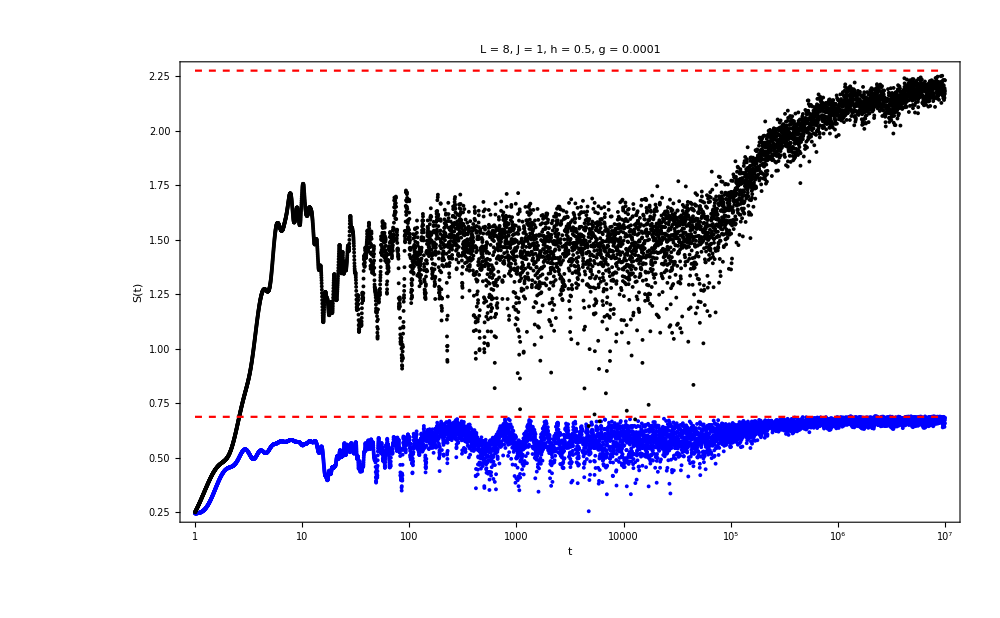

```mathematica
Show[{ListLogLinearPlot[Mean[entropy1],PlotStyle->Blue,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],ListLogLinearPlot[Mean[entropy2],PlotStyle->Black,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[{pageEntropy[1,7],pageEntropy[L/2,L/2]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

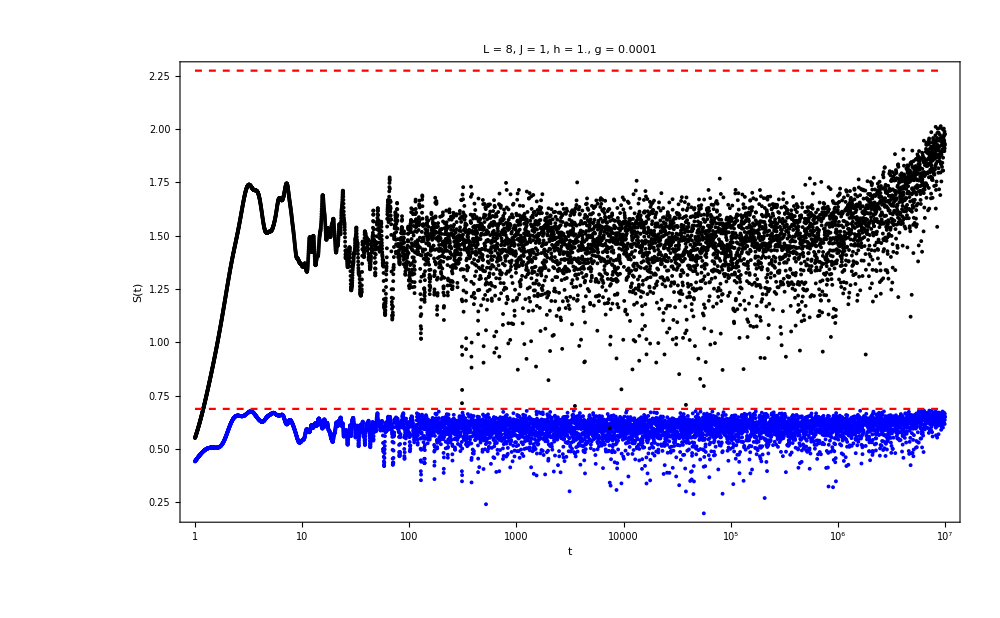

```mathematica
Show[{ListLogLinearPlot[Mean[entropy1],PlotStyle->Blue,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],ListLogLinearPlot[Mean[entropy2],PlotStyle->Black,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[{pageEntropy[1,7],pageEntropy[L/2,L/2]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

## Cycle

```mathematica
J=3;
h=3;
```

```mathematica
glist=Table[10^i,{i,-4,0,0.1}];
glist//Length
```

41

```mathematica
tlist=Table[10^i,{i,0,7,0.001}];
tlist//Length
```

7001

```mathematica
c=N[pageEntropy[L/2,L/2]];
```

```mathematica
plots={};
Do[

H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

allstates=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]][[-10;;-1]];

(*entropy1=ParallelTable[{t,new[j,t,1,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];*)
entropy2=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];(*plot=Show[{ListLogLinearPlot[Mean[entropy1],PlotStyle->Blue,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],ListLogLinearPlot[Mean[entropy2],PlotStyle->Black,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[{pageEntropy[1,7],pageEntropy[L/2,L/2]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All];*)
plot=Show[{ListLogLinearPlot[Mean[entropy2],PlotStyle->Black,Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[c,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All];
Export["mean_plots_L_"<>ToString[L]<>"_La_4_h_1_g_"<>ToString[N[g]]<>"_.png",plot];
AppendTo[plots,plot];

,{g,glist}];
```

```mathematica
ListAnimate[plots2,AnimationRunning->False]
```

# Schmidt

```mathematica
glist=Table[10^i,{i,-2,0.3,0.01}];
```

```mathematica
Clear[schmidt];
schmidt[ini_,t_,L_]:=Module[{schmidt,rho,ck=Conjugate[allvecs] . ini,d=2^(L/2),phases=arrayt[t]*allvecs},
rho=MatrixPartialTrace[Dyad[N[Total[ ck * phases ]]],2,{d,d}];
Chop[Sort[Eigenvalues[rho]]]
];
```

```mathematica
values=ParallelTable[schmidt[j,t,L],{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

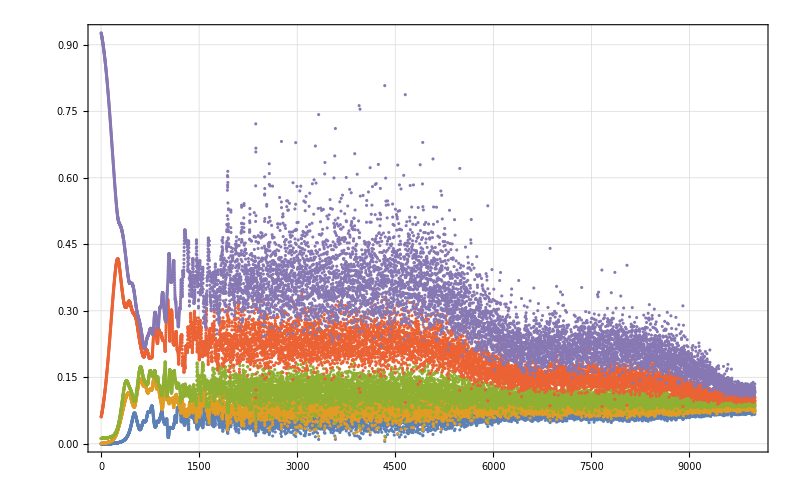

```mathematica
ListPlot[Transpose[values[[1]]][[-5;;-1]],PlotRange->All,PlotTheme->"Detailed",ImageSize->800]
```

```mathematica
values//Dimensions
```

{5,10001,32}

```mathematica
Transpose[values[[1]]]//Dimensions
```

{32,10001}

```mathematica
Table[Total[values[[1]][[i]]],{i,32}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

# fidelity

```mathematica
J=1;
g=0.5;
h=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
Clear[arrayt];
arrayt[t_]:=Exp[-I*allvals*t];
Clear[new];
new[ini_,t_,L_]:=Module[{schmidt,psit,ck=Conjugate[allvecs] . ini,d=2^(L/2),phases=arrayt[t]*allvecs,phases2=arrayt[-t]*allvecs,psitb},
psit=N[Total[  phases*ck ]];
psitb=N[Total[ phases2*ck]];
Abs[Conjugate[psit].psitb]^2
];
```

```mathematica
allstates=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]][[-2;;-1]];
```

```mathematica
tlist=Table[10^i,{i,0,5,0.001}];
tlist//Length
```

5001

```mathematica
entropy2=ParallelTable[{t,new[j,t,L]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

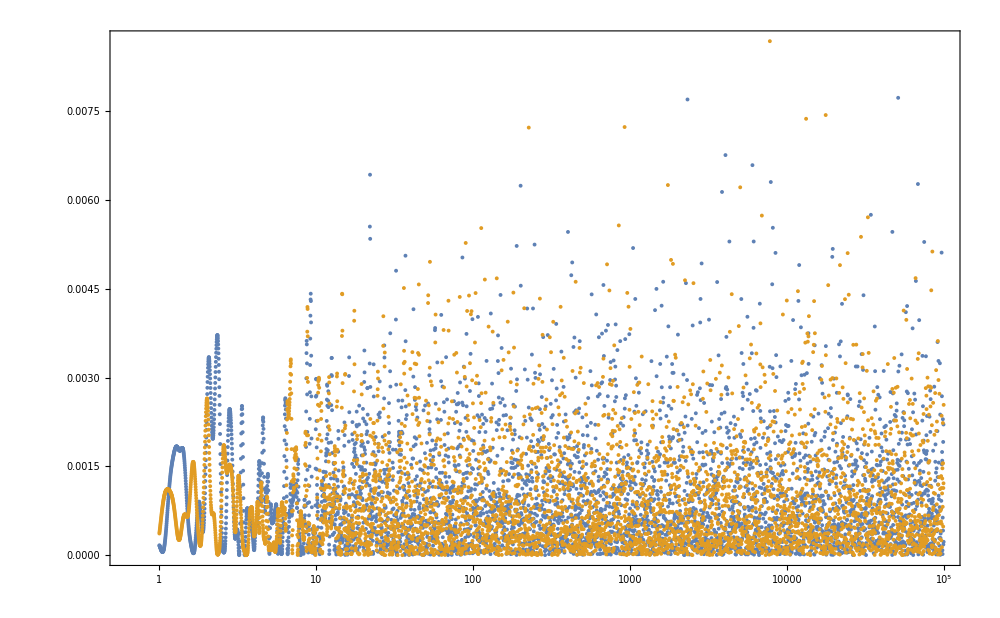

```mathematica
ListLogLinearPlot[entropy2,PlotRange->All,PlotTheme->"Detailed",ImageSize->1000]
```